## Problem 1

```mathematica
Integrate[1/(Sqrt[2*π]*σ)Exp[-x^2/(2*σ^2)],{x,-∞,∞},Assumptions->{σ>0}]
```

1

```mathematica
f=FullSimplify[FourierTransform[(1/(Sqrt[2*π]*σ))Exp[(-x^2)/(2*σ^2)],x,k],Assumptions->{σ>0}]
```

(ⅇ^(-1/2 k^2 σ^2))/(√(2 π))

```mathematica
f[σ_]:=(1/(Sqrt[2*π]*σ))Exp[(-x^2)/(2*σ^2)]
```

```mathematica
F[σ_]:=FullSimplify[FourierTransform[f[σ],x,k],Assumptions->{σ>0}]
```

```mathematica
F[σ]
```

(ⅇ^(-1/2 k^2 σ^2))/(√(2 π))

## Problem 2

```mathematica
FullSimplify[FourierTransform[If[-a<x<a,1,0],x,k],Assumptions->{a>0}]
```

(√(2/π) Sin[a k])/k

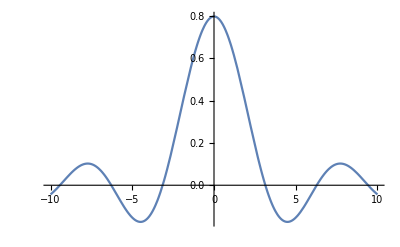

```mathematica
Plot[(√(2/π) Sin[a k])/k/.a->1,{k,-10,10}]
```

## Problem 3

```mathematica
FourierTransform[DiracDelta[x-x0],x,k]
```

ⅇ^(ⅈ k x0)/(√(2 π))

## Problem 5

for convenience, we will set ℏ = 1 and not worry about normalization to get a qualitative solution

We take an initial Gaussian wavefunction in position space

```mathematica
ψ0x=Exp[-x^2/w0^2]
```

ⅇ^(-x^2/w0^2)

use the Fourier transform to get initial momentum space wavefunction (p=k since ℏ=1)

```mathematica
ψ0p=FourierTransform[Exp[-x^2/w0^2],x,p,Assumptions->w0>0]
```

(ⅇ^(-1/4 p^2 w0^2) w0)/(√2)

in momentum space, the wavefunction in free space evolves in time according to the following phase factor

```mathematica
ψtp=ψ0p*Exp[-ⅈ*p^2/(2*m)*t]
```

(ⅇ^(-(ⅈ p^2 t)/(2 m)-(p^2 w0^2)/4) w0)/(√2)

The above expression is the momentum space wavefunction at time t, and m is the mas of the particle.  To get the position space wavefunction, we just have to do an inverse Fourier transform to get back into position space

```mathematica
ψtx=InverseFourierTransform[ψtp,p,x,Assumptions->{w0>0,m>0}]
```

(ⅇ^(-(m x^2)/(2 ⅈ t+m w0^2)) w0)/(√((2 ⅈ t)/m+w0^2))